```mathematica
G[z_, λ_, n_, M_] = Exp[-λ*(M-2)]*((1-Exp[-λ])*Exp[λ*z] + 1)^(M-2)*((1-Exp[-(n-(M-1)*λ)])Exp[λ*(z-1)] + Exp[-(n-(M-1)*λ)])*((1-Exp[-λ])Exp[(n-(M-1)*λ)*(z-1)] + Exp[-λ])
```

ⅇ^(-(-2+M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))

```mathematica
Simplify[ⅇ^(-(-2+M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))]
```

ⅇ^(-n+λ-M λ) (ⅇ^((-1+M) λ)-ⅇ^((-2+M+z) λ)+ⅇ^(n+(-1+z) λ)) (1+ⅇ^((-1+z) λ) (-1+ⅇ^λ))^(-2+M) (1+ⅇ^((-1+z) (n+λ-M λ)) (-1+ⅇ^λ))

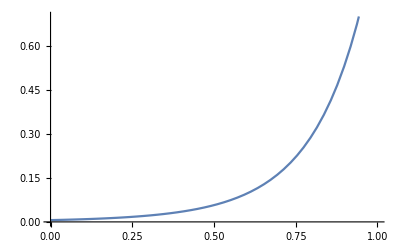

```mathematica
Plot[G[z, 1, 10, 10], {z, 0, 1}]
```

```mathematica
G[1, 1, 100, 20]
```

(1+(1-1/ⅇ) ⅇ)^18/ⅇ^18

```mathematica
N[(1+(1-1/ⅇ) ⅇ)^18/ⅇ^18]
```

1.

```mathematica
CoefficientList[Series[G[x, 1, 100, 20], {x, 0, 30}], x]
```

{((-1+2 ⅇ)^18 (-1+ⅇ+ⅇ^81)^2)/ⅇ^200,((-1+2 ⅇ)^17 (-100+381 ⅇ-461 ⅇ^2+7+20 ⅇ^163))/ⅇ^200,(((11)^16 1)/(2 ⅇ^200),25,1/ⅇ^18,(1/ⅇ^164+28+1)/ⅇ^18,(((2-1/ⅇ)^18 (1) (1)^2)/ⅇ^164+29+(2-1/ⅇ)^18 (1) ((81 (1) (1))/ⅇ^164+1/ⅇ^164))/ⅇ^18}
 |  |  |  |

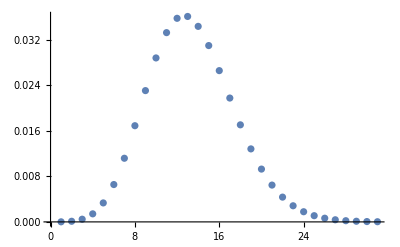

```mathematica
ListPlot[%18]
```

```mathematica
g
```

```mathematica
CoefficientList[Series[G[x, 1, 40, 5], {x, 0, 60}], x]
```

{((-1+2 ⅇ)^3 (-1+ⅇ+ⅇ^36)^2)/ⅇ^80,((1)^2 (-40+10+5 1))/ⅇ^80,((1)11)/(2 ⅇ^80),55,1,1/ⅇ^3,1/ⅇ^3}
 |  |  |  |

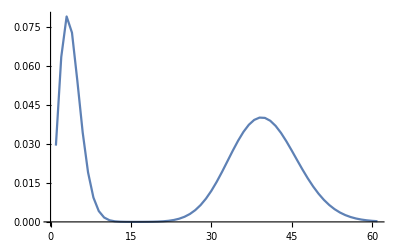

```mathematica
ListLinePlot[%4, PlotRange->All]
```

```mathematica
CoefficientList[Series[G[x, 10, 40, 5], {x, 0, 60}], x]
```

{((2-1/ⅇ^10)^3)/ⅇ^30,(30 (-1+ⅇ^10) (1)^2)/ⅇ^60,1/ⅇ^60,55,1/ⅇ^30,((1) 1^3)/ⅇ^30,((1) (2-1)^3)/ⅇ^30}
 |  |  |  |

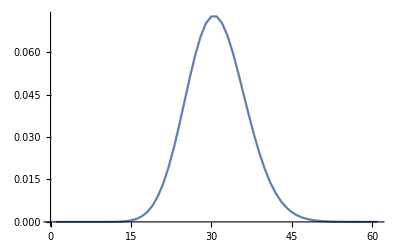

```mathematica
ListLinePlot[%6, PlotRange->All]
```

```mathematica
CoefficientList[Series[G[x, 0.5, 40, 5], {x, 0, 60}], x]
```

{0.222104,0.205124,0.111598,0.0459713,0.0156265,0.00457482,0.00118397,0.00027559,0.0000583931,0.000011364,2.05358×10^-6,3.76995×10^-7,1.68251×10^-7,3.52427×10^-7,9.60548×10^-7,2.49351×10^-6,6.07516×10^-6,0.000013933,0.0000301824,0.0000619484,0.000120803,0.00022438,0.000397863,0.000674881,0.0010972,0.00171262,0.00257072,0.00371625,0.00518096,0.00697468,0.00907746,0.0114344,0.0139548,0.0165165,0.0189758,0.0211807,0.0229878,0.0242776,0.0249679,0.0250223,0.0244528,0.0233161,0.0217054,0.0197385,0.0175439,0.0152485,0.0129669,0.0107934,0.00879804,0.00702604,0.00549938,0.00422054,0.00317717,0.00234689,0.00170169,0.00121157,0.000847316,0.000582247,0.000393249,0.00026113,0.000170529}

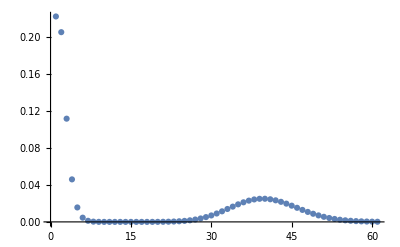

```mathematica
ListPlot[%8, PlotRange->All]
```

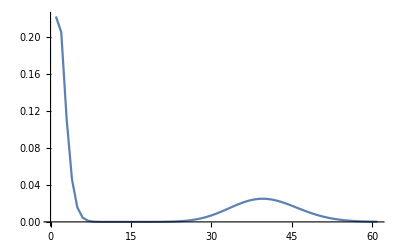

```mathematica
ListLinePlot[%8, PlotRange->All]
```

```mathematica
1-G[0, λ, n, M]
```

1-ⅇ^(-(-2+M) λ) (2-ⅇ^-λ)^(-2+M) (ⅇ^-λ+ⅇ^(-n+(-1+M) λ) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^-λ (1-ⅇ^(-n+(-1+M) λ)))

```mathematica
Simplify[1-ⅇ^(-(-2+M) λ) (2-ⅇ^-λ)^(-2+M) (ⅇ^-λ+ⅇ^(-n+(-1+M) λ) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^-λ (1-ⅇ^(-n+(-1+M) λ)))]
```

1-(ⅇ^(-2 n-(-2+M) λ) (2-ⅇ^-λ)^M (ⅇ^n-ⅇ^((-1+M) λ)+ⅇ^(M λ))^2)/((1-2 ⅇ^λ)^2)

```mathematica
Simplify[1-ⅇ^(-(-2+M) λ) (2-ⅇ^-λ)^(-2+M) (ⅇ^-λ+ⅇ^(-n+(-1+M) λ) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^-λ (1-ⅇ^(-n+(-1+M) λ)))]
```

(ⅇ^(-2 n-(-2+M) λ) (2-ⅇ^-λ)^M (ⅇ^n-ⅇ^((-1+M) λ)+ⅇ^(M λ))^2)/((1-2 ⅇ^λ)^2)

```mathematica
N[G[0, 0.1, 40,5]]
```

0.796689

```mathematica
ⅇ^(-(-2+M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))
```

ⅇ^((2-M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))

```mathematica
D[(ⅇ^((2-M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))), z]
```

```mathematica
ⅇ^((2-M) λ+(-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) λ+ⅇ^((2-M) λ+z λ) (1-ⅇ^-λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-3+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ))) (-2+M) λ+ⅇ^((2-M) λ+(-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ))) (n-(-1+M) λ)
```

ⅇ^((2-M) λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^λ (1-ⅇ^-λ))^(-2+M) λ+ⅇ^(λ+(2-M) λ) (1-ⅇ^-λ) (1+ⅇ^λ (1-ⅇ^-λ))^(-3+M) (-2+M) λ+ⅇ^((2-M) λ) (1-ⅇ^-λ) (1+ⅇ^λ (1-ⅇ^-λ))^(-2+M) (n-(-1+M) λ)

```mathematica
Simplify[ⅇ^((2-M) λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^λ (1-ⅇ^-λ))^(-2+M) λ+ⅇ^(λ+(2-M) λ) (1-ⅇ^-λ) (1+ⅇ^λ (1-ⅇ^-λ))^(-3+M) (-2+M) λ+ⅇ^((2-M) λ) (1-ⅇ^-λ) (1+ⅇ^λ (1-ⅇ^-λ))^(-2+M) (n-(-1+M) λ)]
```

ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))

```mathematica
z=1
```

1